```mathematica
(* Solving the harmonic oscillator *)
DSolve[u''[x]==-u[x],u[x],x]
```

{{u[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
(* Same with initial values *)
DSolve[{u''[x]==-u[x],u[0]==0,u'[0]==1},u[x],x]
```

{{u[x]→Sin[x]}}

```mathematica
DSolve[{u''[x]==-Sin[u[x]],u[0]==1,u'[0]==0},u[x],x]
```

{{u[x]→2 JacobiAmplitude[1/2 (-x √(2 (1-Cos[1]))+2 EllipticF[1/2,Csc[1/2]^2]),Csc[1/2]^2]}}

```mathematica
(* Failing to solve the pendulum equation with damping *)
DSolve[{u''[x]==-Sin[u[x]]-1/10 u'[x],u[0]==1,u'[0]==0},u[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[{u''[x]==-Sin[u[x]]-u'[x]/10,u[0]==1,u'[0]==0},u[x],x]

```mathematica
(* Same numerically *)
pendulum[x_]=u[x]/.First@NDSolve[{u''[x]==-Sin[u[x]]-1/10 u'[x],u[0]==1,u'[0]==0},u[x],{x,0,10}]
```

InterpolatingFunction[{{0., 10.}}, <>][x]

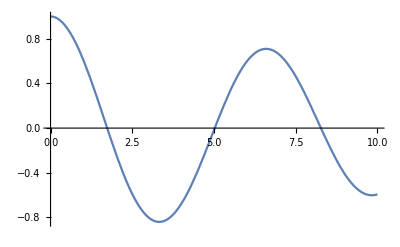

```mathematica
Plot[pendulum[x],{x,0,10}]
```

```mathematica
(* Boundary-value problems: nonlinear diffusion *)
```

```mathematica
diffusion[x_]=u[x]/.NDSolve[{D[(u[x]^-2) u'[x],x]==0,u[0]==1,u[1]==2},u[x],{x,0,1}]
```

{InterpolatingFunction[{{0., 1.}}, <>][x]}

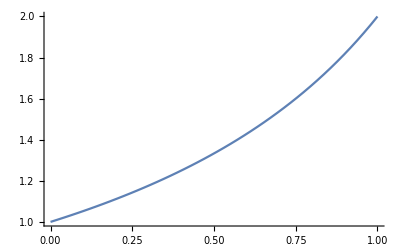

```mathematica
Plot[diffusion[x],{x,0,1}]
```

```mathematica
D[u[x,y],x,x]+D[u[x,y],y,y]
```

u^(0,2)[x,y]+u^(2,0)[x,y]

```mathematica
(* PDEs *)
```

```mathematica
pde[x_,y_]=u[x,y]/.NDSolve[{D[u[x,y],x,x]+D[u[x,y],y,y]==-1,u[0,y]==0,u[1,y]==0,u[x,0]==0,u[x,1]==0},u[x,y],{x,0,1},{y,0,1}]
```

{InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][x,y]}

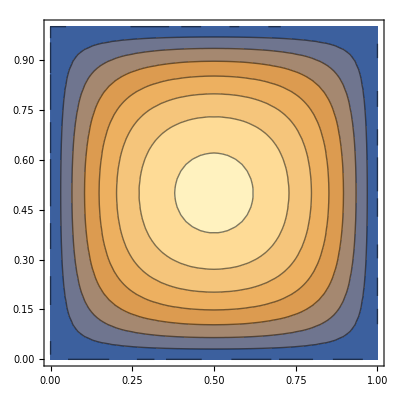

```mathematica
ContourPlot[pde[x,y],{x,0,1},{y,0,1}]
```